# Breathing - Plus Mode

#### Animation of the breathing - plus polarization mode of gravitational waves in f(R) theories. The notebook generates the corresponding deformation patterns of a ring of test particles and associated animation via the geodesic deviation equation.

```mathematica
$Assumptions ={x ∈ Reals, y ∈ Reals, z ∈ Reals, t ∈ Reals, ω ∈ Reals,α ∈ Reals, hp ∈ Reals, q ∈ Reals, μ ∈ Reals};
```

```mathematica
n=4; var= {x,y,z,t};p={0,0,α, α};k={0,0,q,ω}; ω= √(μ^2 + q^2); (*p y α son transversales hp, longitudinales: q, ω, k*)
```

```mathematica
Do[η[i,j] = If[i == j, 1, 0],{i,1,n},{j,1,n}]; η[4,4] = -1; eta = Table[η[i,j],{i,1,n},{j,1,n}];
```

```mathematica
ηm=Table[η[i,j],{i,1,n},{j,1,n}];ηma=MatrixForm[ηm]; Print[Style["η_μν = ", 18], Style[ηma, 18]];
```

η_μν = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
S1[z_,t_] = (1 +1/2 hp Sin[Sum[η[i,j] p[[i]] var[[j]],{i,1,4},{j,1,4}]]+ 1/(6 μ^2) A  Sin[Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]]) S10
```

S10 (1-1/2 hp Sin[t α-z α]+(A Sin[q z-t √(q^2+μ^2)])/(6 μ^2))

```mathematica
S2[z_,t_] = (1 -1/2 hp Sin[ Sum[η[i,j] p[[i]] var[[j]],{i,1,4},{j,1,4}]]+ 1/(6 μ^2) A  Sin[Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]])  S20
```

S20 (1+1/2 hp Sin[t α-z α]+(A Sin[q z-t √(q^2+μ^2)])/(6 μ^2))

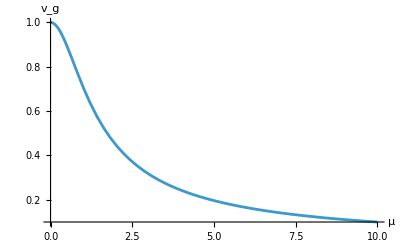

```mathematica
Subscript[v, g] = D[ω,q ]; Plot[Subscript[v, g] /. q-> 1, {μ,0,10},AxesLabel->{Style["μ",16], Style["v_g",16]}]
```

```mathematica
values2={A->1,hp->1.5,S10-> 1,S20->1,μ->1, q -> 0.5,  α -> 1.5}
```

{A→1,hp→1.5,S10→1,S20→1,μ→1,q→0.5,α→1.5}

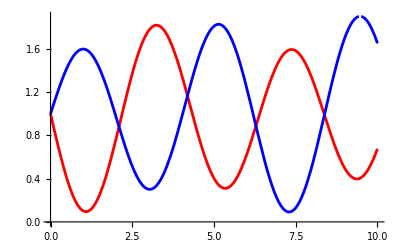

```mathematica
Plot[{S1[0,t]/.values2 ,S2[0,t]/.values2 },{t,0,10}, PlotStyle->{Red,Blue},PlotRange->{0,1.9}]
```

```mathematica
values1={A->1,μ->1, q -> 1, hp-> 1.5,  α-> 1.5}
```

{A→1,μ→1,q→1,hp→1.5,α→1.5}

```mathematica
solgen=  Extract[Solve[{S1[0,0]== Cos[θ], S2[0,0] == Sin[θ]},{S10,S20}],1]
```

{S10→Cos[θ],S20→Sin[θ]}

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[ParametricPlot[{S1[0,tfin]/. solgen /. values1,S2[0,tfin]/.solgen/.values1},{θ,0,2π},PlotRangePadding-> 1,PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{S1, S2}, GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed], PlotStyle->Purple]]
```

### GIF - Download

```mathematica
Do[points[θ][t_]= {S1[0,t]/. solgen /. values1,S2[0,t]/.solgen/.values1},{θ,0,2π,π/4}];
```

```mathematica
frames=Table[ParametricPlot[{S1[0,t]/. solgen/. values1,S2[0,t]/. solgen/. values1},{θ,0,2 π},PlotRangePadding->1,PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{S1, S2}, GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotStyle->Purple,ImageSize->400,PlotLabel->Style[" Breathing Plus Mode"<>ToString[NumberForm[t,{3,2}]],14,Bold,Black]],{t,0,10,0.1}   (*rango de tfin*)];

Export["\\Users\\cindy\\OneDrive/Desktop/breathing_plus.gif",frames,"GIF"]
```

\Users\cindy\OneDrive/Desktop/breathing_plus.gif

#### Dots style

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[Show[Graphics[{PointSize[Medium],Black,Point[{0,0}]},PlotRangePadding-> 1,PlotRange->{{-2,2},{-2,2}}],Table[Graphics[{PointSize[Large],Purple,Point[points[θ][tfin]]}],{θ,0,2π,π/4}], Axes->True,AxesLabel->{"S1","S2"}] ]
```

#### GIF - Download

```mathematica
(*Rango temporal de la animación*)tmax=10;
dt=0.1;

frames=Table[Show[Graphics[{PointSize[Medium],Black,Point[{0,0}]},PlotRangePadding->1,PlotRange->{{-2,2},{-2,2}}],Table[Graphics[{PointSize[Large],Purple,Point[points[θ][t]]}],{θ,0,2 Pi,Pi/4}],Axes->True,AxesLabel->{"S1","S2"},ImageSize->400],{t,0,tmax,dt}];

Export["\\Users\\cindy\\OneDrive/Desktop/breathing_plus_dots.gif",frames,"GIF"]
```

\Users\cindy\OneDrive/Desktop/breathing_plus_dots.gif